### Temporal Memory - SPMF Sequence Example

Peter Overmann, 24 Jul 2022

This notebook demonstrates how to do sequence learning, using a a temporal memory  based on the triadic memory algorithm.

The present algorithm is a temporal memory built from 3 triadic memory instances, wired together to form a simple recurrent network as shown in this circuit diagram:

-Graphics-

The original temporal memory algorithm was  intended to process a stream of sparse distributed representations (SDRs). In order to process  separate finite sequences, the state of the circuit (but not the memory contents) has to be cleared between sequences. We achieve this by sending a zero SDR after each sequence, which causes the circuit’s session variables to reset.

As test data we use a set of 730 sequences with an average length of ca. 50 from the SPMF project:
http://www.philippe-fournier-viger.com/spmf/datasets/SIGN.txt

### Temporal/Sequence Memory Algorithm

```mathematica
TemporalMemory[t_Symbol,{n_Integer,p_Integer}]:=
Module[{M0,M1,M2,overlap,i, y,c,u,v,prediction},

TriadicMemory[M0,{n,p}] ;(* encodes bigrams *)
TriadicMemory[M1,{n,p}] ;(* encodes context *)
TriadicMemory[M2,{n,p}]; (* stores predictions *)

overlap[a_SparseArray,b_SparseArray]:=Total[BitAnd[a,b]];

(* initialize state variables with null vectors *)
i = y=c=u=v=prediction=M1[0];

t[inp_]:=Module[{x, j, bigram},

(* flush circuit state variables if input is zero (used for sequence termination) *)
If[ Total[inp] === 0, 
Return[  i = y=c=u=v=prediction=M1[0]] ];

j = i;

bigram = M0[i = inp,j,_];

If [ overlap[ M0[i,_,bigram], j] < p, M0[ i, j, bigram=M0[]]];

(* bundle previous input with previous context *)
x=BitOr[y,c]; 

y=bigram;

(* store new prediction if necessary *)
If[ prediction != i,M2[u,v,i]];

(*create new random context if necessary*)
If[overlap[M1[_,y,c=M1[x,y,_]],x]<p,M1[x,y,c=M1[]]];

prediction=M2[u=x,v=y,_]
]

];
```

### Configuration

```mathematica
Get[  $UserBaseDirectory <> "/TriadicMemory/triadicmemoryC.m"]
```

```mathematica
n = 1100; p =4;
```

```mathematica
TemporalMemory[ T, {n,p}];
```

### Encoder / Decoder

```mathematica
Encoder[ e_Symbol, {n_Integer, p_Integer} ] := Module[ {code},

e["END"] = SparseArray[{0}, {n}]; (* using this to flush the temporal memory state variables *)

e[Null] = SparseArray[{0}, {n}];
e[{}] = Null;

e[x_SparseArray] := Module[ {s}, 
s = e[ Flatten[x["NonzeroPositions"]]//Sort];
If[ Head[s] === SparseArray, ToString[Sort[Flatten[x["NonzeroPositions"]]]], s]] ;

e[s_] := e[s] =  Module[ {r}, 
r = SparseArray[  RandomSample[ Range[n], p]-> Table[1, {p}], {n}];

e[ Sort[Flatten[r["NonzeroPositions"]]]] = s; r];

];


Encoder[ e, {n, p}]
```

### Import SPMF Test Data

```mathematica
ImportSPMF[ filename_String] := 
Map[ToExpression, SequenceSplit[DeleteCases[ StringSplit[Import[ filename, "String"]], "-1"], {"-2"}], {2}];
```

```mathematica
testdata =  ImportSPMF[ "http://www.philippe-fournier-viger.com/spmf/datasets/SIGN.txt"];
```

Number of sequences in test data set:

```mathematica
Length[testdata]
```

730

Sequence length distribution:

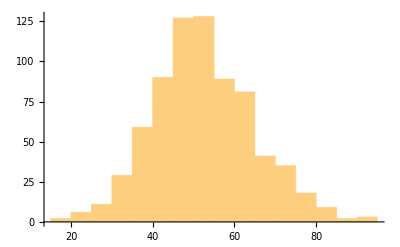

```mathematica
Histogram[ Length /@ testdata]
```

### Test function

```mathematica
sequencepredict[ tokens_List, print_] := Module[ {pred, row},

pred =   Most[ e /@ T /@ e/@Append[tokens, "END"]];

row = If[  #[[1]] === #[[2]], hit++;#[[1]], miss++;Style[#[[1]], Red]] &/@ Transpose[ {tokens, Most[Prepend[pred, Null]]}];

If[ print, Print[Row[row, "   "]]];


];
```

```mathematica
sequencememorytest[ data_List, iter_Integer] := Module[{ b, result},

Do[ 
hit = miss = 0;

Print[ "\niteration ", i ];
sequencepredict[#, i == iter] & /@ data;
Print[100.*(hit) / (hit+miss - 3 * Length[data]), " percent correct\n"];
, {i, 1, iter}];
]
```

### Test

The dataset consisting of 730 sequences is processed in 4 iterations. 

The algorithm is continuously learning -- there is no separation between training and testing.

After each sequence, the algorithm’s state variables (but not the memory contents) are reset.

At each step, the algorithm predicts the next step. Correct predictions are shown in black, mispredictions in red.
(Note that the predictions are not fed back into the algorithm to auto-complete the sequence.)

Mispredictions typically still have an overlap with the expected SDR, which could be used to infer the most likely prediction. In such an advanced test setup the prediction accuracy would be somewhat higher.

This algorithm has only two parameters: The SDR dimension n, and the SDR sparse population p.

The prediction accuracy converges to 95 percent at the 4th iteration.

The first three items in each sequence, which cannot be predicted by this algorithm, are excluded when calculating the accuracy.

```mathematica
sequencememorytest [  testdata, 4 ]
```

iteration 1

2.47428 percent correct

iteration 2

83.4349 percent correct

iteration 3

93.4746 percent correct

iteration 4

515238928133866142932172633187722427413511411181327813671761372534143691444724558246242534251

413658797722682622746387053321131171181326713366136711435195245363724610162504225320252830

442605821136926721041631429173718224466234027254664533511311411711813268133386513669143195245246122504354253242830

5152081924407223162126382748665318113114117221181326513313667143131444217536179180191245586424612253444951274

4824569836324212562950951160911737182268236726415646885365113114641171181326389133136921431952456124616250792534549545725934

41926637162956812757983107511131771822317323141546534311312117118133143195245452462505025336384125932

11860841095717222262728235935146955787911056117118139514319924534392466122531529

148822284751318819102675172377627613550368141164411011711813279139217314374199245402462025325293426267

195073263527753111222364130132578679110421114341171291181201323840133375513624139143162781791801849189190142102452463325348255175866264266

2616851420815492710471828174034195822231526416373150354541132303813342491362114455245242924633253512562663943

1033506287172460185692192212482614927376581414551445811064711355117120111321335772139143521447721824576246542536873259642612628286

11216317186620506022123923122634027374441110361144711712061211319132133485813645139143144622052453124625326646

415668197111569171822202329262127463953371131171181331361431952453524614250505825328312564045

16465411468589531032601730182261262728525933572911311711813313613719524524614250435125321232563438

167684324651331860953103461172918227642627285235593011311711813265133136661371952452461525043512532425639

110510625160512297183830679096486113161921724181976221426387393426211045911411712361321366513914314421824549558489246202479824925332748125969

1374085110311712541625553698226497011194511501121746182054572165113224158272843611411812038132391334472139143144832182453235991042461424963662532355256752578992259

17894399111417194757842729596010499711401345181084623362623727107413111063011411712013232341336613635139202914316144762182452592246714772495625321502566268257838425943

112012122461471781811396710981011173761478871569778865107199120111112227923139910326708092104271172837303831569311060114621279713264133688913795139161439017283181102219223632453910824612253259297126081

1345282495811667514535617495718822251262761386377678087786411054811411713255133139501432192451520357924659622472532528712558625968

418275717819342052602226243336376411011439117132354013914325209245163051592534245257

4733819391163817184120566622231032265406842783479481112737114461171911813244137143451442521424515526425325729

1707352838821619441440481737186022354623272657454739366850787959114132114951133752551361220137143144245134254652532425725919

419928199811495771941746691860225323612654629056113209311711813295133143195245304475822502535558257363725951522628588

13839831134172232627114137144245524322531018

1575823651824521329171418222652731351133243114461174412734411322513330137143144481451683324512164925342

1162456608501394514465717518221055232263273133393529364211315321153811771204113314362814443145371491502454424725319264

135702273237789819337110241716188022112342658111011711813271367313914143199245153840247455025329259212626169264

127703818281771112419182212237261101011711812029323943139161431447819924515404124744462483537253262546426621

1313734647826381127361361714184319221239511311713241513613713814316351443024525321232587

2232581793111304113181192722710263912441141181322413313814324525328258

41960812968221623176426127463559533111371171181322636613362136671952453334250404325325258142642930

1841122356882169103336606411851322144950767717233765181111926278748104531132011713254586271136596166707813752141143186451893819124512412523025325816262

5185581296110581114171152260264656531131171186213257133146195245132731250354325323242582624549

1037343653591181237466974131922171234760482011313273133721711791912456524638432472522127253352574926271

51433819361142941671738183572223223162627374669531101144073117341326513355136681397143144571711791912092452424624739252424825356632572021

2129374152054166821389731034111431481712324318195522264645534269354023783247911073311411712013271136396813914317119121024527246247252472535965257

211192014831401724181043272326123536168478889111114117120613314414531491501624179180131841902092372453224624725728

13456427298183013395214912173216194922511262353171425078798488891112311310114117120713313914314414561491501621791801841891902452462472572425

1503515910171822271105411812413952144571992452632362461224742572126242

11365813717230182660231473457532911311711812031024133195245247212225035402572624349

150602830492791211131428171518581922231026573135367320787934841688891101143211711821120613651139714314416320924542552463824725729273

19273853782618504341334417487942113113216206366761331521626775146414924513562465764253404525828262

19414420627822829261305827494839765311021113148111715133133713677139181412836143232142454755246459662534245257258332627079

225143324152126131351336419274411320114125512016132133191377141814414614915032163172452462253258102624852

1431571712231026541183344145113126351324133401362432137141143132454243485224682532592125

1486524147838133614151752418562252264275811413649171924525329332592123

1495424245834462027482623531511313214221333214312144351912454125224253333625919

1020221126521513174142319492753485113811711325051133122814314432191245940253313526624

41451829591132521728185622261465453113331141172911813255581331341433014634401491952454245246152532725735382592123262

2121743647827955113254301856221414633531131142848117291321331341614319524542246713253252573539262267

225314142136458223295611351712849465311334114271171332433441354314123195245246616253257374126250

2252941582191235111328321710182023264144110111114141171431443436209245627253

127342496048910356847132336676917153761188031193042411139485311051561175461186413213933141714318162191209212245292475825279253212614345

103841131924176251848231142722505341141171185213351434916519124511152522533033

4101681924253217201837596922232656277541152135484370533311029114117301187213271133139631143144173391841912122451260652525054253261

195681047182327283254353673201105111501174813945144199245612222925316262

1112083106551718642327242841353611011711813914314461199245153225326240

4485182230379601315551721869639472340462612765114193411711854132351415014415343172521812455102466225321

1424421655361826459217013273217184071762251592325603741304311410117118132141336314468153551725658181245662467112531925538

161694144354452853973106081155417551886197622406823392627884156727462787982110117118132711331413780144424792172841812142454959246299625336271

81719947521315461118150113132484913314119124531344124641425225324272713637

83244976831320171018475311311327913377143781912451529312465158247482526669253252625641

214168242891832371521261734204447231227225239504111471171118141404624511194825325

82329932451133531728203147112262716303536403948111511411724118132461411431821144131520924510253

841531167811762192026483675321141511710118132767814313114452571532538172396018119124518657224721302524425349

1505821221822419641156181960274728532311311861132141173151143144591721812544191245710492471426633

8151895866105171682260276728323523366372347831110141171181395714114319924519442532626249

2187081975111525477117446534826522011351171181324950731331435114414615327421846919119524524625056672663140295

4225681968113653171418464065113117118132386713537411436619524525331257444825823272625962

2505643849834958111718612326127352839334412463755531101135711411710291181326013334113921141143193032195214245253252572592026254

4446083997511431513231740182864222613116293536413346715367195578779661131143711727381181327273133141211436144195245510253257502626526325

1331711511117221816862778677635563681114911172113214141197214314424525267424651612533033255

1317371018472214302362611127503133433529364911414141245252465253

814194454923291315535517491837602036386252612746311235108283421136511528117133331431114445145211491501652217018423724324439245435259246253263

1125411105117618417224421105011813948144199245272937246253192591516

1559621117121823853262761284435364110110571171186013246565813914131437144199245404624633253212625226713

41479819881043771137173818842235782334278946446547678053361131328313369141421441952451655622533925568257455026285

221334345981965103269171218802245672344687727463558477253113132133154863143161957624556253255617125740262

1347281016978321142317224188271262728553549368041211101276117118139701431447719974245462493725326261

210245363425298144934713968113517361877223341233245692642272846507073387847791137115481171181327213337143201441952451958672534325754259

212298193910761301120415775175018471422324106131267827351503713545910253971101141173611833132808190921532831182981847318919199134209245253056612477424816253491162616768266103107

22170819741069137116368153031172651183515722582357278639894482466478473259110871147794117388813238113613341398414113814316517392120184191245291252473693253100103116261266

2293166958122224323954940441061047103171811211231426527374128466955681101132512011713220105108133104146901653038881843318919120914245912476567253562667884

1525627696844659601141989113221662266327127394753597478798448117421321721133141155814314414677971496117319124551102246342528525328329091271439495

12732217194145812203346559576211475815104421863221423532635611115441171186013259141211444851245285425326138

13288815241732518100239862612710239199173729078577994245404156708424625326176772714748

281212630921363910321356601723501846682014245759153727285861355366673865784979417511413269701411614314476245552465253192614547262

8172392435113368859980187510819606792203759267927763916506474786211052561131344114721091174557132154713321301415814314434712451438889625332657325555

411681733963701580837418912228778123687226647327414467377879110611171181271326513914019141101431162144692192451457102253253085909425971

136372202648194813277594411610801081158781534172838791812019741095272232947733922777092107761191117111332651141241176612614125461431448424559631012534085255

1617726338569391946652028452627754835675311110231141172413269133411431445019124552602461225237253424725832

492049618144287222557023111926277746684829531131324347133426714476191195245412461621250522523031253333725825

23132826927355736182539233112114221171191183213234133616143144145814915020162141841891902454302482531128330912310

3315233510481655537112221131117133291361419141361432030147153444616718418913245911394024745248272521821253242628330947

233335262927434818645371131133135013654143105114715149916746245422465112474524825326924

11165117102091426127183911061141346117118124215013613947141521438491442420924535372532554043259122643132

158641711873202326132728334079351241291101411711813265661395621436314470149221991624542432533234255454625929262512643738280

1040531141915323917120226142326362749723347783079521123111312013213329451361214346149150167245134125325255259182126434283309310

1040651513417351872202526142731331939519110221176118120132666713963141143641471314941994521044245244125330259464726254264280385028549309

153558172718622213261463856533311311432117132161364257141143144345195245114724625319242574428454309310

11426517371869212428221329261464353401131144111711813267136491415143381475014915055161181232519524534526624692532572811461309310

1536541732186220122164635581131142711728118132591331434261611923181195382458455024625332532574226228148284124955309310

1541511737201021261272535131936405924671105112113283411411711120221322133181433144145147161498150291841851891902091224546248332554850256273283309310

1512233149176291826352732110848117111850120139314314419924591424255256202623928013283283094

10377115313617221875207382612747354352412825110661171181202313965141721431533319969245444825554256402626128028364309

101618235815192217114540261341465311212113151176136391412137143338245313625225543442562527280562835130952

10265217192749201141511341171322133513221361814333514439245253212425542284343091231041

1037551520361771861132826427413533110811711186213231395414121435144199122451932253222525542262472806428321

1042581583617137186420422122652728435935932242910140108110656117118139143144199245132330253255262502831457309310

132841179185522114226127352331363811413216434614115471432452531924255392804828410253094031030

11417132437118502039226382635213611313241441413154814345144291672457102825123253142554328046309

111018132337173195020122143626427353311413216414314115324414316724572829251253255283284213094031024

132755171870221558261334735423660113132561929311414720285914332405316125245143951251434625324302806328123453095631054

11141135573174218842033225275263427873211493119485713224127174141143581439701682454043472517225328028435683093169310

13318517618972016892227884266927124727482119466612028331321034364410710814151137434780109143104144941688124530899398253626776255322605228177862841930931050

111121317821890207214251221638587626839522735362867157810792911311493111723119120132338313330141344984143168542456470748124919253562553228454161309310

112327154456173818306120129465726621131411413281241321258141310161431445416818124548343945253284

1156651372731522341719356618862017426162741331102811437117142913232139141143361684720924539442534885281496730931025

11152745531337441217281862012362630233532404711311711850124161324813329143251441952452424649253142572834230931049

154651174418632016542672735192436314711342117381185913245611331432391448147431491505719524541246112532572835630931066

1133175183735173623163410184189190122458243125320

11323613547617224618408320506437492627782838351254752694871531104511171121141421117121181202913213313674791394414372144851456814710149443150161638173184918919020921024524422482522535728430930310

35510363037477295347312781113117118133136143145149150331682418428189190322453212529253141725528411309

1152741332511725201539234450264402753285435845363741584669551101135711711181209141327072133681363139491433314414514734149161503871163168179184189190209212245252642532812834828419309310

15133717518452026427356113642110117111843132222313639139281432114419924532424710323325316192801238309310

1029471518281712602094326127583746110625111331171185612011132484913954514314452145149221505016838184189190199212245721242531636262283312843093101451

111016173182220132652723351836394511011831127151325557133251393237143192814441147624149150291661671841853818919021224572464251253283284404330931050

11526917451880206026627753515365667110911751184912716231323434413337421391229143301472114915047184189190462122452831627024625324482552845561309310

133559173018672014332368265274073243664724144621101016111601144854117155118221202113234575884851391114347501442092454243246822533127137281728330931063

11232913304817141855201226427332812351536463847531106117118341201013231321391431444514740149515016751184189819020524524625239442532128474930931057

11151343581773918276322164226105535812364045465611011711184712791324113938143144531476501491501674521841891902052452324633252253202563031

143617818433113323564241101571781791144111171181613223813914314420924572725321

131218173283115351361973117827930111101171181413346143144145714915018491891902452129253

1314371710184131113573647155373786791133411781183813212401331214314451451499150168201742317921180191245273225216253

86934382011322627291035136110531117118139143144199245222531315

131245146917310185423549262273147353653151131118132481331431441451491501681805119119524532246162504252202532426241

4111918105363173277233364263127741935123628411145117118119161326668139714314472209245292463746248342532555261

5163981911423044172518552328262427522915343536411011061133111722118132454813313914320431441454145321491502092453824621247495025333

1450591744187029192231152332358363741520110113261171211183312510161325657139914325414464145149241501631317918020921424539424752246624758253263

14481710185731253512362868192378167929110151111311761181512138132471339111391434441445320924532333740246247253259

2205241896622105526272943533123423512361105581171181217111326164139561433571441992453445492466247253242551325918

1226481097420115926727712923333512364011011711812125132341393239671433144721992451518536124641472532661324

133195141030171181052022292615273639336241476694531105113671145961117561189712521132125896133139891436414410314565921491501912092452454609124867252697125375768087

51837812944132540146583176249912022506426139272921543515362467476685531107611133411711812345132841331933811391160143821441451495815016317438871801912052092455963252717825351

8374648639657713245314951051718881122022176786262723479010687110114495211711893121647013226210713961660688514343611031448991149781501741801912052092453950832462833252981022537226975

821295162142155171820154272911357361106114117311815132535813951435014420924543844249222825313162613940

461281917132374188131192635362941486268737869271565779110571171181213033491325876136314355144116024539445324610152532226526932

203841263227463116351236306733787943110361171118132454713634421431442209245232844246492531518

13338827944131742121855205264731163635114145536762747854797711010114465011711812724132407213621231391431970144252092122453763253565925526614

12450811960132055171218671651262275931351036563761831101185712540132535413658139143314438174452196245437277247725332656825926621

1173687159451416641870226402627311135413744431101181215125231323839676813934143661441742821924533596225350542594626619

141940171118472938351036434641531131143611717118441324213323143391443214637149150191209824531246252253242625812

142917104413114118913228136214472456242531113

311627354936110121131311731181912510151323233133136139714381441814514961501692452024825311

5410819201412421771848291336353946531101131171184313241441331114340145146150451681742619120924525322473825225319

1444171018532072622715311133356364658110911111711185613249133134213914384314617418419120924538246247253270

1323621718722212162642729212831363542737879441101171118125301326365139858143591442068209238245455424834253322592723940

43537813094611122974781766618428920502240492627924753635560655164113108111711812131411328413328143514414614939596115080195245214824638712535426276

12818251820815435372962423262945714027323139351936414642671103711344117381181327613313914314471462565149150195213245133459622461721253

517824329144043311526351036291131320117118231212213244133191431442447145149150163181841891902453324825526312

1155481145173182072622731132535536110443117118132441394114342144471631424199245303224862553325621

11466853125383519365911061117118121283313263133213913941645621431740145231491515046163411684243184201891901992092452554425626626

81117938451310414182016273133353639464053511011814421491501637191245212225212255292561516

85793540133114161842202233226273929163310361111171181113314314414514915016317918012184189190245424817256

9371431521722201123122627351829364050713979471105112192111411713251139814314424209213122453243253255

515748313581819165727352364068110166118132139663143641447119924523254449248172533825526254592662932

52757813141531819513523364711011813235254136551391150143619924517203125326255738

11334917185823113272535143616323719434415110411882212225132511365213971434514421324538253242554146

41103654172318583750110316117118221325657139143144192091424525325255313843

14761838112646171418562327343512363037737867911021131141911731122222413245601435814629149131503318420924594055253265

4114546698359228213536817341892207026277516367911011212117118132215838613623144153561632117262841811841924538457424965712532530505826511

2037392344492630402752353136421101221181201317132511394143471442454146714915010184818919020915210245253

56265848976143769173018205267223346261472778352839367434542979110311711812132441221613245707213914321441684317918021041923245592532551268

463456082815414371735212468229261827110162811271111336471171229118521201324950676913333481367013914314532149150173382101524556622485125325525

891425302016612612768735178791101143250117118651191721293513263133139423143242831144371461491501713353180561815218919021061824525360255

18791197017187620682627351516362528735178671101181326972136751391431992451233374350253255522663

8169587911343559741755518402012262728703646681131073117118121132475076133136511431441463233195245152530525725025345266

811091926132751141761867224120311141333361432456024672533444266

112433171418442836354746193269267879451105117113914319939201247102125316

527368940111817742202612835462269347816791104301171184113238391391431441992476253141526224

53336810953112217184828413552463471639110643117111811921324513942143199245262472531426229

4125245483961105511264217381831283512366741446822781332795894212710550108109110521171181192012313951143561711992453339247725326243

536418309511450173218533511143481340982028108610911211711833121162713249133713946143471441461491503121424725325426221

11141813294517419529841108810951112711721181211225133271393042143128144145261491501711024725335254332621521

101214132852171151858356233698471081095511232117118431211627132515313321394914333501441454146344814915057153171247725331382542026240

921110192013374114426017518623515323654487983810830109110612114241171118121291321395814333914414628147571491501714918059247253404625426256

9413222614445217840183435521364650319843108291094911242114101176118511212530132121393814314414616149150171179180247152533725420262

1191013263446591435451711862205829274873427832796098857108109112435411411730118121132555613313936531433114414615017121415247425325424262

11181949831430311792097565174626378797098167610851091103847112331171341185012013281133139377714314491145481466114915066153411755320924540246722482558426026228

570808529951112156479142526404417616365618294920315023685127982810811094511011711837121221323839818313935143144598614614915018155612092454324671248255852606326213

558638399791057651116201438421712143182359265527355036569810851109731121147123711734118120121441253213264139296214330144751465354149150171214217692454041248253262

921361139401358711481711018842043702637273035674859773986572108491098011468117118120121121327982139691437714641491501712934521754146245332465461248626026264

941511717143341218552045262527351932365156596010124521081010911414411812113254139349143501441456147531491501711752918024524624882603126243

11511466751716018567935404736649862681081091126311450117421187012063046731327113919556514348491441464114714929150741621713139180722452328246572484255260374326261

5477483398310416811131422291761530182326362735126981564998751011086410911221143711731118120132727313340501395963143134511446714614714915084162465217166175384320924525246586524825548542603926219

1040531114232483851715418975258264227713576843632485698821011910867010949114411711843120122513213331139506414351591463374149601503716217129245246667524859255260412627787

196587614172426285464367372226378791141011711812713260139659143144711462349149150245214548249422533426262

12754895814181722112628102935363462517252782479110118139314314441147131491502454382493225326244

241681950521547171874487879133111914314426146411491502453445246314253202431

41959819632857364718565365472237879113117118132231331214314611581491501952453335246162504043253202729

1145589611335172518642211572627283753303611333541171181335114324521461491501952453124622504025310

11252458695513355117261828114430343611349117118133501463149150195245246250422531422

41529551035431317245325442811463012364854567413914321144146491492150167181912454042246372532234273

157684647848976134969172918743710381137011732118771273413267133661361432435195245422461225025323263025919

165083051435362672778211046118143444724528246253172426612163337

1144848528630133135736741104111711813910143314424533372461225323272661620

1544894930435361104211813933314343144452452327246253162026529382661013

236381971153317221830558353669374774627911019118571191013956144651461506621024511246232725342255492686

11070815296817618306535364142311051911711811913322251392114321024516485024626253323942255556226811

152652284089214172304203536372446441945561101811811911139614314425210245122462325331392555058268

4144960151458171862281924292538303536413374656787911410161171182012537136814153143521441221924548512462126253255256

15324356583497015691718712210262728383033373966411929746479110331117118431192513236133446013921431442182212451358612464025320234852259462617

25264812140966145117391828102641305335114211061171186012515221393214314414663149341502102452933246253202526648

414795328364614754721278791131171181324950133143145614915019524521242468250324125313172562530

1596489421561172018284829133035313663465853541134011738118125251326013341571433214514915019524524616250452532563439

11642435869632360802414264328301535103671110411171186611912013371364857139131431442182453968246112474749253225925425955

19712621127410143853151219172018236210824551265212128856588086301649647193107359505972873639109414411011861120713248139471411131431773721924532103246682842532163254676925675259

1201098911710737994971362661510817678098181981222665241625273060353689486310753525411334877811059118119281244151132558139571436470144912192452462532984869226072

11450457698519851067729091135861395215162582831726536273181121910422125627296871305435553648607623817879102110511565117118801197124451322139614336414421924546922462538626066

11247799646172848749109136873144255175618105198094221065266627286370304490354571366976237811011362931171181192412152132601331391441455791149401502193245921012467253152189265

124404816179632244262765301442353674457879641103253811543581171011841123233112513239139143181442092102455161253482551112

135542958152737171822283526306243425367311012117118124139211431444221024511324625343259

19264335582757301329353647114212811711851124610132311331391114314446209324543522533740

115364377586983134152175188428302916351011014113201171181234912413246781334553741391431441461491501952453151542471921250572534225511

184995214172442628230153533678110481181202113939143402457272532591126538

11232895514243013203536474853541102711311728118119211321335291432144146311492515019524562625039253152681719

11619822022931391432471728353353110271134411711812012143463445146714952915019524523252504025325525810

1144782953151219171018224826427461354110118612021241443191245302521125316202585262333926823

11027829332326631141181323132133514314428146251497150291841891902453182531216258

114528295815125317182313552627473350285463349639411081094611411551117118571321331114314414632149150451841891905619524546222503525320258262

4876053511357117111812015221325859143561461014915016831801912453643246192624725284525317

41148152224206626286443539369484059533154110711113291171183412012132616213916143144170191193209245246224752252372534347

2386141831911135214281762918592210262745303519393632483358531101181201325713931435614418418919019120924520252462472523725343

111244252835832594114233615435817203718652210262747293063946531101171184212013132626313334139143144384014614915016316821184189190191210245312462475961252452535055

412158794310303613164561148081173762222829387135391137211813225791332414314414573150245232647552466067247248575925331258

4149960106974134148142223171234183176304765264527773646353255411011329681171187012020132212872731333744143144321451491501631685117320924511622465724719253258

2374942834821359561332144515557317235018862413627412930401101173111812310161327172139421432214420475120932454448246761682472485425338258

215394344660831449156913142670871720326218529424114268886427482836532141110611711882123132491393014347144146149150163502092452223582467383247656725325840

2153235537182446911417813571475153017485818842355723680110422113547011443117441187312333391324552626313361641391020143211442774145146149471502976209245828824631248625325525851

125445981045596879232748261766281622303162353669414367450607871101134711732118127143121446524524624247612485556253

1517281418382461243572611327593016353631442011011811959132535413614420931024532475024672472484142253232925919

44121611512011825245672433253172591113

2415183615401737221939262743293542465373781279501101113117120361331391431451493817325191193205245910302532825918

15532171183546315354113430117118133329143145149150341681731911932452202526925313

1528391725211926231562738301135363346375373187879110241131171181202123913314314414514614915017318019119320524532531620259810

361620465315331151121181331014414615150181731801919119324524222532716

1341441724114301461016149715020173132453253259

245504103984014517328635474653541131171133143146149195245162461922250253323625927

4841194914208017102219262850354634533271557851113115291171230133271952453144247525457596364702503625323

51833596086579381311434204221026362156779114120132474856581431442454154253254

15562228311001168326365869129111181318611479981799140196990211081222368261291273577117125368595110571157012658120713236641361392959143601272458488107253768293101128259

27679415278284850122447524337726343143353236135771205578674110711317231171181213123531327280133182113951143115256681441535469179180245382479253162925630289

225504181751579135863143018432422662615372053417179191101181325556139161431442456225334392544246259272657

4112830379214651132181647232632768411771557973110113341172011819491202913210616213336136384514375914425482092451454632472494025332286

2405783591722144633234426347312781110102011156114365111755211813247133431364853139131435414458245185525519322563741

1323336556384121651647094014351823271022466606944452873110111117118391206813237621395661433424531536524772532125264147

128448159552932171845242234261427513536425411520401171311812023301323331332114331144714614941505317324524624825325543

2142389364828505924395126276417203511115521171311812032401324314316253814456146531491506817334245492462124837253292555558

21228384793063741136111711812051601326513327143201441462850149150173372454449246162324836392533125556

8243595771375526252767343658691133248114117161186512056132596013928143201444166146149141501734045245492462324839432532555363

135362125410681338236980245758263759278910167104108391099111016117118701205055132333443451333213666139426014346611447816317922180209532112462477284253

83644968831377155363173564188721707924462665279823801145397678719711010601151173671186212040132463132821332813613916143129336114486163251741792266180210415821122773230231246247253

174768133467935398669155462173663182272246026436127538244454087787998110121176118124475613243133668813328139161914320296414411961631748317968180209412112277123065231232802358524624725384

8151993742135476174618812272233424672614568271490357366244281081097886110543117118551202913221331213673139143144527716330174801791803421021125246312472535925541

10931172183770114278617334245252541622

15294017185324204126827285861351021363238445451101152511711852124712132121391619143144187189131903324524631247922

1415821124474788325993013396817271875252635313654677649447911023117311828120384312319139143612162214416318420211891902102455166246333724746248272

12343895524124426275811064111711851124151322139101437144516311171791802018413189190211994520252210182453032353924826240278

126508119601429551719186211010491174118591241336139541437144163201995220120224540434653246303424815

831793850141718203516364911355117118621231013259611335714325814463145113914915017113195197198245472482502327

11418819229455235133644514728531554113121156117711856124132495013314314446145391491501713819519751982453324717250232526241

2232950578104513224015112171854242735411362511091131619117118124313247133139143514414614915024537246303424725921

1413244117191813472328262711520117118401249132213315143812144301462514915029245254

22226412168517929141331586756183773195254244227346041254434535535978467911011113328011712043681322869721333066139143144752102276523224661247332533840

41318829231443661739712251652627724112444530685778791102411331117251206913217013337139143538405256671443210227232246592473225336

561181916204042263627454172244272465478796011011431651171182513914314424175209246213525349

122734687041319820629404253243126739355841444511011291133711711832132313916143303814464821024618284625350

475583969204867241141266422773114478011739132127778133455914354374144722455624619342534651

515296011471743248264272937564445114117143351445057245422461221253

129398229493126192768324078217955114244111711845132434413628143234214424625333

13447826955213541102762113336516068377824796411330451141171186513624623253

513967688609441457174018642445522638275911413254561431446117450246123725343

48526411015311112421788322662445264667271007269897910112065132573339848611913641621171411231271431032406387118121170708117788179821811891909124558991052492025390

5984811051417194566391827754463223334261020352948654236741138511813267681436697214417040601731771796118018164189190245768187952491623253

56838191011416174365371824741915632230312632277335394688973666446178387970113132641361431441701731018162189190245869324920253

51589751437407276173359184482193426275643113117132454678801361214347144641731771813818930190245222573246485424725341

41448778095520264924176163218572770311535693625525960113811171325153141791435075144153232451473253

110911023437453725102182238101986146675175918811924879026307627931141326143121447817056177641796018169189190245258410025374

1717349308533714426817361820456724265276365621141171327014366144495824544482462925333

259624121852927101316171825232241482614353054120132505113361437144177181189190245323424632531224

16265422849928194457241121267382763361142311713259611431442453437415324610253

1030601725186822242642511535273366293448782344793911071172118131206113262143144416917332245502462824736372531920

445528409551348861741189522274926593761856441388911071171181321913916211433914463761455114915054171421735210232453170802461424725364

130371121202585941217668981838609014257172192320811102251642639772711728343521364115443455633657468619211370788879118621321391436316314421024553100246247757625382

59168219371852441245551107117118171215658132541431441732224245332461325328258

471581919113940132427172818482249535411036113232611510161171182914621149150311912453846246252252533225914

21718811922541262195126276329351436244144214557132591431442453324661025325258

49178124103741132028525515294218634858535464110511349117141181326513319143601446814550149150168222533173321912324625335394726927

2364983095811120171318724193226122737744678107954110511711813214359621444209246625329259286

2124586949133244172718262939742078794724523246253161925533

5717819231040451329566716304624195326275948281101211721181363313914331414450147201491501681793718518911191245435724625225253353825821

217638131036442225552645475253155462114491171181431418144461471491115019124537482465252232532931258

10414413182817129515023531154521142711720118491431619144431912453646246525332272

5125455483893159111527401728193726244839744113120204113256143531441532464253332572592223

1303556148239224024381718471937262769782979491135812013253541435214450561532464125334

412853708439371941472211262757233633344044454611312013250511434952562466546025325725935

10141542461323315662177163247243926827494857535411011333117291183814312144521454014915045171371912453524662522225329259

225418229471538441045110611117111824534246253161929

517545584791311304517185229403510365114716421491504924532462462532128

438468339571324481712185822394411322627376251452911011434411173111815501211331433014414736149150153181421891902452463253101623255

41220829301348171855221050261274128293545442511011117118161321397143144193217351791802461525325525936

147485918837226019542612276228143544349362053584146564434245401106117118120231361514311144292452461325321255

2354582995711152185824194726122756303436421116131171181445246172340512533225515

42023819351328365459172446184267221941267483456531101121113295811711864133255713914314414530149150621732717915180661912454424625231322533740259

41927893822185826794840533111012113347111712811875133631391725143111446714537701491501734372179180191245652465253454925926933

4374683095011122913324917518622251262765351036331106311171118121434713221363439139143144445315348173211813845189190209245246253202325952

420258933134256173718642235262747110381134555117639118611211012713344541391434014458145435314915057153141733217941180601831918911190212092452462325334258259

2203281293722185726112763351436435546545361110131134049117533118133471391930143311441451491501731621394819124524625323269

51521892412522627613944174511130351171321359601462247149181505017340179361805324611253332582538

21552879601116511718582430262737295035365967537879611111019117411823139143144246485625342255

22263218274468303778257994341082310912019132213335143311442424669253282591416

1212889322426302227362935347231787938941082010937120191321431714423332465392532591214

22323826212751723137787947104391081091201322341441431442946246712253252591617

4586183238469661113413398217352272772665271653544969374578247911164117311867120311325506813914347511447711911224524610142477625220212532962

13436461782792240193338247122631557461625531354287078297950903710830109111113211311711812013256133143144191246514432522325339

57438195210313817241847223226274446653354727825794994353910830109501136012041132143424519124613252202532936

223235262127464115441345724078297952941081091202443132143281445024661033422533125920

23040819945222532261527509410810956114421174118521202113243471366162441143171441464414915017317918037184103418951903924613253

2263582394822341227447278207953942940108211095511417421171181201843132471362414316144511461539149150601732531246143225328

2535684628363935324237144844124511417431171011813315411439144501461614911150163174273017931184261891919024654253257292592023

201613794044245511202113222143191442424671225334257252925918

21555869612042512634275437156451321435214460245485324618253364025729322592124

21332869431110177183729353639245253424625315

4228193113215325317291859261925276505828353841364652110117711833120132313923143516144125624524625345

494581621965262775374754446070244978117910818109531104311176117501181201213248139101416614331441473164301791803420923624539248162825357

41209261915254345273741224429701678579902128108109341106117118120313981431442316411179180321813918919020923624536402471325330

242458349531562174818681146271171118321202429132636413943141476114365661444617718151552452467222472625352602543640

4164181949151157711750182654602766110134411711812021326913922431431444515456591815520924540482462324725353622543135

316396365815795115451740263827556229523534365611011117118431201325813918143454144446115418148209245322466142472425341

4123981952157131718212644492761281035365111038117118120111321462139143591441642154181475020924524725343562542430

311491715454726182731394146110251115411711829120812132495113919231414852143111442824524732248

215378695313182511714352942736545019271631113561201014314646149150170472452475248202825312

1566582098813232917151834262536276483284278353169546379761131171201413289133328514124143861641814548195245512465250392532625974

13048491182421572623273537443645782279110117118120131391714312421445220924534246624715192534051

414328193715486017381868262431273642295535621101011340541171181322133395313928301432314434145149150166561844118919059209112452224625358

4139945225052262827653644413529585747596063685178307911037117211185413213943143144622454266762461524725361

2345282896235615365567465053354703139782079498214831019105108109611104111111744118431202413264651391431445168145481465714915015371712224521272532556063262133340

3541336414946104053554441051638108109511147121171118151391432144431718392451925253263425542

313594822182658702757848839658044604511010511116311711856120629139125214381445516431209112452424653248171925364732543649

34464411183991869222627452810351936110117118411201237132401391614143701433816415202092452324650248253546325431

263136274755351730461024536541051110831093911025117118139528143214433146149150153293716812184823189190245248172533843

319293282518351411391721482242262755284361346535468457879561117113851141172304014384171162454124724815232535163

249523637041238395893057791545531718562227263461113258411719120425513282143781444424564246248485125335432546871

1364742782895415324917185321462610295722352333111591205013252141551432453841246122483425325445

1394171723123182326794615386917336518472137402671327503529643642120132451431442455224624248253302545659

1344335657425826442230412747281635323623454911111812013246143144245246714253212543842

1193189412722914357363914114462453033246122531723

117398139452915351136442453338246162532226

31215419388116948141718222643492753612823403536110711711842120111321360631392114310144411545218146502092453424725325430

412488395915567717492627576346254553215469365578796611013471171118139281431445120372456173246102503125320232553950

41270819802233262428723533646486953435411313267913345771437417819524629382505025342472625971

31139242615182760682845593530364621485316545169387811311117211812051332914382514467195246248392504725323

47335476824998222404426342741434546567850525553110361111211133011731118471321013377139143144195182092463725024682536162

128353131987249234214656615515517475818577254222126274460363741345454373506478797611033113117381181324013914152143481442112462032247596125353

244474132840938511427481558821718498919612225261654538728313641464511011373117115011881132139141528014313144941535521024629692472536064

415386397815094910414476917326118552244262835413934455346657860548011036113295911730118132515213356139143481511791801952102454273250243381253

4155881967281635364610525355473781136111813314417344179371801952463425018244825340

4165081962102448171856261925275261285135364671131171181326013314358144576319524615202503725329

41645869551423311719184328103554648730105221081095111344117111813256133531435419524625032342532526

244593158409116641435636456825477810791103311711838132346265139123014331144392033224642512502531620

255704941815251194962264427374328383539584853110740113501174611845132139101411433472032456324612250252531822255

4285187960134466173218835035365848311104911721185413257578139154714311014452203245576724625038253142552430

410568396719627226542783285235153663674824851110711363701171181327576139143575877792032456171246122025031253242554350

332494168279165519536126713483143694146634440457021110371171184212071781326813911351416414326514417114179180195203524551622461025025317

311091815384617355126545927657228374836554131497871479425711045111530761171181325013947141536314314473203246235225025325534

4157965103137172318432854366246425071167867984110117118561198312013277139261433814449531952032462061722502531225535

496581792151662220442634573772772286035573670486843747834881107117118132711394164141851431449119520324549532461676832505625325

3124286951267112845351936466944787950113111511741181324849133143144151273917923180431952502932253

37398194822242625275228323536467318447811791115234511342117431325013314319524617250382531012

1324321828852995222134126627533442353611021113401171184512012205758132561331392314342414414514915044195209724615250313925311

475181962282452351336614622486930567820796311011171132560117518118120151325813313919143571441952466250322531626238

2812453523656465416927547818796111361171132581337143571952461520250113925325

4104181951146441718502627422821433511364632113117118132454713371431441952461316250253

1133284941142340151718104928223435163647461269307879113511171185813242451331431952501125325

12036894726192427344128354622113117171184212041321331434314449195250253

14122417618352819263634461353254391131171118291335143144153319524510

4922528406170812354477414464917421856254357263827326210243541367151597879661141171205314444245642461524825325467

41565829741042461116331469861712346218549328633533679416475783711058117118121132613261921393156143579014467195204246222505125325544

1737441059860113536456117303718672239235445026640272833414647701978793211038111142911455117481326566139143621445368164421952042455458246925025325534

177784105086395420612655305735463647483453110117118601325213358136751392914327214470195204246196825014164025338

594581542812223127443532336415846406978327956110111141711771811847121242912567741326613963814346414415195204102461948250113325326

46223844812992853112148591432173920422326312730563545364170135278791131141011713333581431446024625325834

419121445202823152126226367011787911019113117118421201713335139143182414427401461491504124632532582534

4394851208324956606993110591740187019461126352768284530553667113114121171313357136521435314424662533325825

414695711471859223823312632272849365634701750781079113114295211730481325455143144195198582451925025316

819289293714110737417631839623536417832791102211311730118721326061133139231431331401441461491506719519824526250385925316

4333951298309521121491712185720102345266275428353650463269785558791131321331434014419519824622250442531419

113047146777172459185119122366265527133592036415846425670254078107911053111431174411857120812129139501431441952032452462502531522

134354121881994628112030364144457015787911111711826165232456312532225

2187496479201061015441114871221773185076792322452635692728941079946561051145511711877119781321439214410315424733253382544981255475261299598265102

123262304081227954103748112236171918575396011350114117118119446120359631334714314455146214214915150561534117918044246202472532664352

110538976202450261527622849543536657046567879671101129113481148611733011866119511208313338134139631143321465814915073195198199245246182475525025319

51049819652059277538688247226474537827971111748117118119120708013313143175351766341912461421247111225327442280

128748169882049722627704775787911419117411811936912080139211431441992012022461324811124041767725322374346255622595560

2104681962115451718542024261527523235366311041117118651194812049641397571431442102451924616247552533826642

11665899310217917121890207626112738819524777894110154211711857119671209113966143144199245402464754247253222858702554546266552813031

116528109731853145777817671681112411711811912076713933143111441992027520932245283135392481213656625342512665463

14231031713374164495511421117611931646591201133581355714118451431463014915171195186181632454447658325356255204025948

1284622127896610547714223396106171634781865803126473548361035070113409211741181193538213345134154497143146321491537119539941972452038432482505264253677225575257

23042820956122554171418643922651131511711937120113353134143101461491532417919245232624811253

238808289911013751485971717618103397935313688221131177119163267701201011332013492143146102149170469418024527667324815253304262255

123558972131567146877631760651266110101111174119461207513961143514471199352102833245223024816253405025553622593638

12849220278796413517014503122351036591105611157117119533120521391158143144199201202682452547542476024825342

257678539711318791411017112332402624274838615631142011712031333334371413536143122102452241472476869248192535061

173842157289941316701496105178918833164823555363821473969955090113117311811912120132485213353134971431462562149561504317022596324574802472481011253606625530

22682813455475761411744116918565312835153647102548811102739113117740119411203133952141511431465514719149191210222142452030342472482525725343258

139758229941116181310214317419314068353688384369777879901132383114841176119120931331514314614919519719824532515924720212534925564672727181

218688598010627113162638497814115273617507286201951817565844822704779113117120133143314614919145193321942453541246247434473252462535661262

2125486964103650117132124145861171255118664831355553674978417968113117119412013313456143146149191245222924624733342523725342

138572273151115892432206810235817182225502612463062143536674274781979481101194139144210452452462924725352592542653

12253213168617966236112183214303510361131147114481177118119120551341514314457146291492415063168281792618059245522464025531582631920281

1172821012344983132995511521841142753110411711943139143199201209242454547246303724825523

2529839421019143846171351832281373644113117119120133134371434146149168179195197198245248625024

122458139571141417519442672753385111311712013314361461214916854179180199201245313924616247255474825921

2191088149115107891111413112231545681753669921829202282873865107111266610327943134357611983132641361412559143601442452468810024724879253502554110625848

2138589921016611484941746223212627313847704878301131171196133135241431462014915359245185873246772535125532

2239282011732144061173318661658698626592785481398453541131141176211943413330601413114310146149168671694257191193292053824522702462482522532687680

2143281294323354926334653411311191513331351461491016817919119324563724742442531924268

1294126148159681122177232026132838452530352131365311351171194043133146149324548246248122494225333

125488129601023711161617218892832753536706378537911377611711811912084133571355813614314620811491501687717918019551971982454450246152482494025326226964

2149111417565313454322329351330392641474474427879114311711950141143144245162486253462554026510

13415217291864313339352736464250444556476284930665317319781279113311711910120135514314671491673416819124524248411253

2555819671053631318401734120261127643273536507333781579618843548960110118119139171512452429248253343726257268

1495284395623542622762488153711316117111191322122133131978135771361214320146171491681417919119324515374524663248525328342551825651

2548812032274131110911817119141391314116211431442620924562229253344025518

2265182013411718332740384430111916113251171322428311331922321431523209245292473425345

136515132582696121521417182232472427633448652866577446787911011831139144292453550246255

23248824961101712186031235735163668110758117111872139131436144302455624625322

23337577082538112617122040354158110711711183413923241439144272452461925336255

1030461716186123687926592953353669110281171313927143111443324550622462514044253286

22945618881546115414363717241974207523262231354841787950110921117111827139131437144245402462532555273

2495082696010247417132034402862110141173118192454624624925253363943

26692855910011681328501718511969862236492627313574781791101011711829134203370143301441871891908024572246152517687253257

2232546698164193011211714203660262731351574247879110117111813912143714424545582466132533925519

22627818934203374312530351636384124327815791101175118281391714314424543592462533725521

2538984699911253313478717134181002026362349863727318535419538110121511374117161188813382139143144146149150912457377246625158652532564852286

14662513168930201024171134472627313756323536381933110711411713328139143146501475114917053246182544825923

2528084311581429371723382055703026392731352125477424787966114621171181331914314414714915024613182532845255566925649

1202122260811102617163019313536403311011711825139231433144292455024671225326614

22231815940112123143558171024203426133639762778791101211411751183013416143144281621871818919024538502462532932255

24961842970112637171618472035235136312160661348110151177118251622224646592532552425641

247718291118231443551727201922405426282432353674347879134331439144451621624539482466253255257

26169842111924134114384017252021224726313230357478794910410810911111711181616215187189121902724545602467925339255

5192011122914637417302357264331333219253435101102111711827162221791801871891902453859246825325518

26775847112024134217123118282123376573261422663219353611411711813316143144162179151801871891902454324625325438255

1506122734822351017194920261130321574407867955110911711818139143514416217918724189190246725348255

250684182881329111417392016222632373541123011010117111815132311391436144245562462532425727

134678279811035112117718782028542671383211431117221344513746691431442456368246616332533025643

231638191020179242614233574297879341115117111813245385024671225327

535388309441118761710204626332834363215192925411141120134142224543542466253254266

52428820935111661171826741337784795124548246610253192542231

115917420362632182435123046537414437887952113911721341314314633191246249342521925327

109191325334952146567171203453232648505141141181619124535246525215182532125724

17295226385505981739609105105614124718222019735272428673641964454454833537478479581104651114117118119161328991971331395214314455191245322466824787248492522532585

249638381323264658142745171618224431195935113633113639114401171133121345014714915024524615253243225720

23256326193235174818531011351141413371431461491702139191246153043252222532428

2236681513305014511719222426312048324935934531131011711334713414351471114919124625327267

111719143781920313346352236524138581101034441111171118681191212613927143144501826618924671225028253253925643286

186124244455556183246779671319821082674273175983562364274978799611011811938431204134508713714424548848811311624618253576468

2851125535584680959106286112236149617568718452023377697266427313581406316256644110743611171118139134214343814424530412465825375265286

116132462171122225261631355417141111171182454325420272558288

23864834973131580171324075353036487423727812791137117133143146101492452524814212533970

2667386113141122220492627313536741678779629750108109133154314311144245382462532834255

24073834101711945231625261131335935273641212811011311711913229303944137641391431814415146164492451325465255

215244163893528205523222634273231143364821536731778117911311711331431461491701912463754247132521825333

117768910157283361353670296278147911011731391214361952462471925327322662124

2418082714191712223070232629711831503251354749435344114161181113714415433191245672467152533638255212574042

184982264055866818416710821315611762197523442127653114733536554939539544674787990110436811711876134501396014338511447215416201791118025191245342462504725325525670

1881198771017381081116135390239913160354092042267418756710778617911311719132118133143161141732463051556324725321226683872562726612289

28195121186861107999103945110124119610913661431781417917164682125202314815526141156316810814715735561403612216673257817913449571131175811970768494106136102137101671461052451631682462475052249120253609197259145153262175268135

228295112821918381315701762250235126313514754878117966113161177134143183271842018718930190246251456125325333941255

1498841721873392510407211243915181930732627313574387879531102211711813914314423246253455725525934

230628241117192326153118543258359553851411474297879521101611711182212271391014314420245247212592728

254688499731327811720111822602330592611931123554079738741081091346714314418718914245502464625325921

2526159108149171116211437222018233136262429354225974555108281091101171181321397143144132462533025538259

21856891017419739204026312432253735365242737879134113814311444924515255334725812

223728151013223917120275726473855401173243578979993667108109113301142911713270133286914314556146149150249725045253325825916

222588141025171918261231203435536504940513053747811791141120133134371431461538149150187211891902324533246925324

2214881395711445279174519392264264629132163510737814113117713324531345414314615471471492456624612249432533825920286

22225477081534931131017138307342787958113611713618491377501433147641491502455624612253332552592128

217238119321069203426243115353629385874167879481141171118181341434144132452467142532725921

1100128872101041116331346941734951910323368926309032553544388341243797581084710911611012117118132851338413914325144147149151501875018919024556246247253454925973910111227931

146672114581055139361737205322231226383142354434097108109114181171181342914314441146391474914915058187189519024725333542581526262

2953811017294231112535526411522732478479341131171341431461492472533025820259232624448291

15584834101516133117202226727942324371354367333781179511131171351411214314675149150152192455670247253395025821

219238159351055601171751336171237612016263114250113271171181336414314414641147149150187246218919024551247253222582625965

1577322324815369281071316171226275331323538405117052147825113114431171181191361431461491503718758189472452472532582026265295

29118515101228133983141173292065264871314235434069731678791137117119211331431521872344245475224725327323725926264295

24081830101222133717123311926353673557814796811311117119120132697013328134271436144147341645424725253255425326257295

51920810923111813244817617622332612342931383536494074477879601101133264117127118119141333065139211431441871891902455824625526428

5394283395113216117142230263145353654492553741943787791331431871891901912462025326832

2182189281320506615491711224826353132517416377867952974010810957114142118133121431472453956246253292563034

225358199431464721722572631207354781079711106117111827139724143144147149150361622824532374624625525641

111626144068171272021233972231356743275364378337959110114117811814715149121501622454457246253283025425518

10172113387562223362619314635862676373287812979711141183014751491501621520245492461125325444255

1213355798163410132030173222631183573367849992754108109651139117133134151431466214768149763246247192534125537

162738401150131917741492224372610382859633143354436705378110151171181391614314424529462461425318256

538120828912210608913203710117902310226399331213210335659436447322337811794511072113871171133139121434145881497424524619485825368961042601062932492

21072831458631326421711543182352643727713111383553651481653547334787946114191245332471225219253

2597443037818381339172522312619352473437879582454524625332342552925736

171968641068176019692231522614531554353670827323377813381106711711881139914314417777245293439505961246725525726156294

2357882713291724223026233128733648796511311209151342455053246247251587125333392564346

1061534361324291445505759172163037513118393511489545317478791131335134414614917021461912452467247222522526253283226249

160100840106313195117522221432654431353664575941743478794215329184273782245147024625362652602538293

1911028681076176719802228582620593125633536757330427879561102462711149117541182913918721431314417786245496924625061256257444526033

281519221089951312791780181111031272684286064312735113637661024457451177375977865123110567011364243118133134143144551467149150173246304910124725320688825581852562525916289295

154628401312176222631357320297897942972555108151091142453724625125316232551125627

1091938391326321451526062174203340533121453511364854373787911371171133814321462314718149170221912462493750252292532552526255

169100850106613214917619632218472648313557593873207879153288218456187272451223842464255253626826029339

17810721035862958317913516717326823266369877415537110455611365117335712213366134139143345914663624589246612471425321297173

16278850133617212232261131351470534211413318710189624525547516925920

2548184198910349917212274852666279431351136907817911059641135011751118133154813957143491447517277981822455824614247162063253382592333

11101121341391581668951131409176104015316813778914130138175490114185318019107115154167221292658116272874109165318384354275100369969117705778417982170921311181191321799417814314410814714117114915024524610412224711253212925485259

112117891291011130172836116352270321097813791261101201251321141391131431952456982246412471525324475725661642592026287112286

17990416368679431073135365176619742249263135442534781511011711841119132374013645139143245186982246522535564256

17628112817251918263135247525354110638117118511325714621171191253101625450

18110544248833669571073131164173651971236326311286355841474424457270788929522537911034113251171181331366214314414628249253213268802558495265286

1119181017693482787911011713914316460195246375224725321322591326255

2388982010172818371922132612331603536817458787911391171331431912454953246658024714293025216253332542427424625556

1248289106413175253196322482649313543638688144624583975010816109113132767913375801466718718552453224612251372532825574

15568838105614291739194726314335364244457416417879541107113117301331399321433314614934152572451537254462554025713

10466613143517136194722263731418395153940743878794813318719124558246122482533033

15766518228639929115813401741195424264231233574347879481101421113117118245602462513237253283025520

115360132530171931202324263235384555444159744778879541101422114141175118271391431442453352246918264

222408698894110631332511721521964263150351236585688591560685774204278437911014113111711812096122161371391431442453339246112533025918

1169142150171102028261932133576787794411011421171202452924725325255

1067317137565444570477831113181323824548246718253392662226

10202857588295134050657217162951597319792266263135466178901101131141911760119243049120146149551717518247246182472725333698526252

1467283810111731947203026311635744278579641136181171182513268711331431442716924563246713362532325644266

166888581063135117521922265331253511461454677478791134711813283861339481431445715381185191245422462024724825229322533980255

2466583910411327301716311945232126143235742236787911311417117120313314612149624559246253342543725520

132453171923292622311835837454449737879521101131911710118341391421143144282461530253255

16710242830817629461019722631643559734278795011012431142117311813274164394918220362458091246616253606325775762604752286

196108523708711078136217166319265228335631693557735075825179110661141111712118120671646024529492468198253772602228659

2294377878194499610708913205010013317519074224210326885636597533461047686781647110113117113914314685149150126171959924524456824649572479825318606412525514

15154845115313194417102052222542266433135147524781279110211132711711971331431462451524825552562829288

1086217138731444553741932787946113134614317324524620292479112531318257

1448221018837924437413351736202131222615322959718151723871645695273347879110611711840139143144391542724557247253256

15369839106281340172922342624313538364445427337787952975610810965111201182714133411431441691872451824625326114

13385825101436177262840312935306955742078277911018113117191331431952452425025339492583426113

1508241836811371017619472638314635494433456470567323781579110711711843136631392914330144741695471176243418219524524639250132535167

1497742635815361017111940343138474433455673234178127957110911711813550139241432514460176321952452462507132535464259

3541035192681127101843135399174420286331384535254636412923695689732278427911093211340117133120413413914110414334100164301737519524524825012164825360682585255

1245486968167695811133374172575198422572650298190315235155336596973787911047117118137143144851473916218440245205577882475625343652633027828628832

191258103513431736234256263727652878963115516521214045442969547324381139110301131171202123133801349013914332811468216234165931686619524558768924768253477172280286

118117812101632134311217332340512627612884110316435653670857319627863799451135846133711347713713937491431450721541623016586185195245568325342676925528628829611

1881052212381064932136197145317541824412615272869983120353684741978110511131175211912013367139121433146721517180165651661762453949250253348225559632628790263286288

1799722257815589107102128133578148417297231195611364776905354697473341107451136011746119251204133611391431477514965162371631696818527391952455525025341596225577992633228628830

158812132186469281022117740631723642076492644312561351836697351785211053711348117381204133139421434314775163121753224534247194750252253254261

18224970349291071728553224363518376953747833113114211714611149166385417061179247141625031253262726026112262606526823280

150634233381034401732193926314635743778137945110530117118120213341139914144491433421445916411221856024524725355

216196510481349927104697112217142182847962330402641318335363893102448645747879671107121131171181201336113466143376214659149150641731424573247432531552255

1486642738810391319172237262531363529742841787960110711721181346113647139141525314331641732451124742253

101365101110177661939602288262861313573517897927113117813340134871391132143336714641147577014936521501695424523389924742432531653642554549257286

185102423288155293710541316451746197420963426277556693550363844325178796811039118481364177139141143144151491732452270952472534061672555357

10619118591133269172207084235666265267313536788173346179501101441135111745120133139143147149471695563187245372475325221253587283254261

11240657187411017282535314551183660707450527837791102211329117231342613533143271461614921501641662472503425319260262556626811280

1557421138844894410203326283135397314367877945110231171183013925143144175434924547532461319247222534125556662563425932

41539572332642620281767351838444125154574497827911011813413951432124662456253

27379412785593410254211171218532250263828162031356365244374571741462781101171181391314314424624547225325539

159674141854146837479287210737611223417355261263327701331236619362544457421787911071171181345813914314424625350

2721094255181252101858138793179777110222642631573548407685447010173336178627911043117111813313911143144153751876796245242466325368

226618599814789701046118717118551979236457713124683536773852634445761105811366117591331341397143476514614962150942452242932532732255

15261232338224294175105362141974841743635023263129351837442047455478796711011336711141173072133381391434146681491501642717034177597318124646253288

27080516208749942105374142241171518195172264027384445507325477879591101131171391331391434146149162245542535871

149688381041173619392615742040787960110731117118139321414547143214424513304425348

4151785931132852861001475185822402630293835213946557325847812799762108109991101135161117136118711334866134139112314322441144146496314937150183721876525154572538825533502586067

1701104143984010561317419421983235468266928163150353739944451087581787910011352661171181334913914314424534478624712252512538025729

269824212885291038174376353236741878337911071133011712213313914319524527250372533967

2546831361374202282122812369123109741351712818832811801293135624364537435870100217875791105611311757133139551411341431479614967150108176711952453924772250848825329768125594283286

42435489251863691051018441453831745102281670915910137424773896954100687420497850997210810982110111131173813313596139143971466714952173195246342472502535566255

4178281994142035121849281316528832315369340223047515553485463696797732633783411010211132114117311829133921368713914323147149451952462475725059253255

1668452846821479921013172315262756598129143543670578278457911348117411338313558141521433953146551471491661952461625073253252553044

1863397310172826623513367040617825796811313322691353364143236514661491701952475249193225326250

118698979104117552820713573680475339546838781911311713516143314613149164561952462337250424825326251

1141018513165260175320542630287996312227353649566971781137117133901356471417714348146721478914973164941663218467195246250253

276774133873958101840284371353736756946781131171181331361731141551433256146531491501952462503925315

1207081097638171864466726402728156635736697879113117135113414137651433146621471494631661952461425025322255

152688379801972262728103635451695371787911034113411172133701397311413863143326419524612250392531525523

11377861772018262948733536703478167911311713367135143349146149166223364184661952464725019253

422248129811025951718282035117036867826791131911713390135143821462114915089195246232503945253293325547

1273141117540458318329511019292623483542363928441131171331432466132532581624

416214648852295410291345881730372628119314935443650794127974077108109861362014311245572462525353255259

59148124107611719212628133122233644352533957154574781361613324625325818

411258294116241330364652636678791713753671886227023762671313520973464108109801361221561415014375116132169851912461015252272533825819

14667213298301071817192631352353114201171184413441136511411434247161622191246112522825325815

1017284013475011841561933232615343135324853259139108121091363014114361872719124652522925325821

4917263182232140102051121934246252811143551536303916447433787913612467253

150548459641034731722194023697426335531375732351658415163447538527879110201171411824648253

2151852748811199531016144159173332320243426253135224445747813711441876246253

1345051422832337471730182631283597294410810949110117118136334313914114319271441872524662125340

231488249551011151761928342026425274315353914534445751878795211071211711813730139143231442464225322

13545516258269522321583118123922514410951710871131181331513628141143291444324538492461425334266

21532687087619371011341345147117435621936225326631184674214878127966113111423117118581333013642143191245552462522534126627

1759586310621481172265265831355538193441456144969767420787110561171181361391416064143571644924512428824725324296673

12039607281440105613194217431834224451269355231153649411245707527781611011731181365359139141143737501446916447245622472534825430

1396321322862396927571718202155266428313536677054782579659916381081110952113133195246402501415253

146702833349761017285165353669661678579113133731351430141143631671453745149231505615119524621322502531218

1769523654812559112102661171870287189351076973785179110750113601171331396141841438514788149481501031516397195245455925065722531427332543742

114423737484398310111728543539367053787911038113471171334513937143414765149150151441952452502532542125

1144936185865099410451721876205464264627752860822913443536695581787911011348117133139743141511431518019524525250682531525422

180978451322811496178219582048264929306088354789696192753378237911011421134501175431336514114344621466149151871703919525051832532425534

5126986107171991163108410911313315113195245235725092531620

1567884598810119117328548035403669814279110371131173813370139161414352143553151467319524619412506025315

41069829171916262935742778136241431515118250222525328364050262135254286

52268817109143411520522672728351670781131171411114314658149150671511952463325012253

1126685101728353692155787911313315120195246235625025318

4183889521034102171528799435513669749078559811011313960117405313364135637143151121952455871250112531419252542946

476481979141335527417481844819970108109801141165117118781336714314415246531611651624561756876179425418028195197198246250497225332255213745

28990887101242175185120268428477835413688695579110611344821171118135481393714114343814414645811491501524916116515175527717931339501802185195197198862462502532225255

57308194010234217185028268129829335475669782579113801141171331351431472714919150161131641654185179143418020195197198246162502532425532

1016741717026781138117133914314615241473641492519963201202246212472531319

2445982396710191712835651456370647879113711713314314643147501491996020120224622247112531520262

10327311183117283547153053702578121131171133561359551431451357146651494581651661454179818019916612012022463924726253293629519

2184486961107217147720704278113511713348135143145146631494916516639179401995620120224628247192532225295

529358269451331551720222523241912362839117415786793311341117111853133274013413618143141467147149161410165179180246253259

5712819171013273948281863223747232632355036421125993810831109581101171183313613916143314434147291491502092452482535125420

25973521388133916401441177224926324570353651995710810911011711181364243139143371445014733149151502091224529248182536225424

26270846101536134817737224526383250354158426610351108109110341171118140143414414719149150210142453324823253472542528

414278393310365970172371923502613840565711063511711841139281431443214714913150209245248162534425420

4182281193510331444681734202823412662910143591083610965110301171118139143144147321491502092452481625338254

1798123742687882858948102031134772173218143822702643927364567434435771016069105213310811109110401171181321391431443014712251495150292102452462534654255257

418258129381020541716192242432615323035283639311101171391431441471491502107246253

13082811131417992263108410911191011328114291171331925139121431446114514915041168321791803624638247253

26110851020815392811631333351721581842196288892248264932292436504115461363913714114314459191245556624625225325923

41361819681131366214416416601791957197198246250312561927

1426821415523278163793110571718192920582641845611111711835139143144301472814915033165179111803424638247672502531344

16694424264957843589401135172519688720885931768167363742568444821017010863109110324811718118601367213934471432314414741149150246122505525339

284898641457174322292623316079355236371422578101621081091331431441472714919150492466135461250253182166

15991628408224110276417201886193761262485326535573836487074837860798481101731086310911011712118133461391431441474214915024691454250253475166

2728284810471418271792819492223263734313260683513533676411584307110163108501114311724118551335214351441472546149211502463951250253

51214294283229204710214513546017114618692843264432526535393641784245913315134114414714915024634250253

2678662936822589501031441417214548232627204157354946745178796099556810810911011771181333954139253314318341446624524647562533059

269924223981459950113036481718373826273143853286351674344778796384408299761081091101511115117611813314314414721149150185577118951190246612504625366

2909651819810689273013501711314026283688353924494123843299771081091101216117111813322701391431448014634591471514929150671877887189721909424543512465363250253

2729041923363754950830446392742541343142617152228314035396537071786184998210810913312661431144751461471018561493255115076187737918967190862454648246760250253

41220869301029451715187628326735253670377826113113311341345614314472147714921501651617522179180195197198247314625025321

250684131552730811631984257717141822242611693536377387058717842792874993910829109133491431446014712231491504118747561891902462475225025348

51025819541917418662833453526365770385178277999202110812109291136117133551345614314630521491501653117918019519719824725025324

170895285381058956671332141931171154225226693536873818517424627879818439133641431441475014915018665187341895919042862461524725025327

4860196813331434172842563536671143811813375914314419510551971982501625319232562530

416388796911171283760353036113511439117133106214314419554197198250253202425626

5106281977112914162117222841633536474557113468114691171331431457149166617921953197198247250244025325615262

1113571711869231454267276228345535243660113511713358134591455014915016636293017593339179251804519519719824716250825325619

108611711875312935367315327433607867976113465114661171335143144145149150165111661751791219519719824721232502533825625

1025731711188223362627752863723135298074243478157945113127111483117113381431441451491501651664069175211794193718019519719824725022253256

6203487957281335365470297818796511342117411813347141485614351441661046179180195531971198247212525019253

51842869511047173792867353677693968782587113114521171133127014314414530541461494191501651416632741751791526180195197198247250212533743

523618199811172114353225019411131279114801171331886143144195911971982472501625345532592626356

49328161103864173118742835367069567879113621172711813316291353058143614472145149150711955919719824752503425325613

41430819331059176187228376035366869446678327977111725113117261181356114314474145641492915019519719824525025311

214188692310375393171382234262746287031354436258841847879110711343117291341132135811433314490145456414672149651501871319189190195861971982472505725340

5163989521014551711869285976354236996092784679110134011356931174111813513929143630145548914948150195571974719824622250253151926273

47528199411678613155017511828618235369538194870638478791011101029113539311749118461351433014419519719824542247625062254232525616

41734819691071318802847623536734461783279113391143870117133501345113519431431441951971982452502531316

421238596711155517187629366035736968782479110611359117111872133455813413544139714175143195197198245102025033

41557819103102414100175818111296793356036697399787911012551136394117561181339297135771391654141596214331441956119719810524548247250253222525542

47478196813171879284059352436706369457823113114271171351171143144146611492915016631179180195196719719824725025315262

51882899710588011192313344517244690152753792649338828528335423610175108109921112140113117144113586143251441476914943150871951971982453824720250253

4136581911112307410317621851125197620323326112740287599355836115476897698410778707911711057113831181331161356313952143531451496115019519719824539247102508225325634

5356082497310182274941351611712363112262728993610669881025778145879114110113117118116133135721051393014320145101149641501951041971982463370250253255295

5131839187394011613161111718130299935753611369109787911015477411411211748133721071436014414592149681501951976619824542247250253193239

44261829985137601490171284566353436826955783979841106191135111452671172011813532751391431441465314921150802451624757250442531147

63663825974112332143964173318293765353171465569406278791102128113117131356614324144195197253255262

222438951102845568113181711946972360264727985368353690705784787911016291133911482117301332013541143144145149118715086195197246247152505925325

442585141597091001072101133661172462181132869357678791106799117231181356595139371432560144166179180109195641972454724734250752533843

46368195110455013173718812846543582697840798411338641146511733135391387143341441456114915016649771791801951972451432250253

58121926107887131561176218117238195722711328743536130697992110205411473904551181081339313614143144195197245250253322544449

2609283291181074113134717148181302210026762712170931117877793859114117391331231356714158661431451214919519724540622476250912531425436

41226727381619337813152752751744183594208123366465293911019113346311411771331353014314414537149253417125526284280

451181922861051375177618112204670239010226318227782883357236118696279110126111377104117133437413514314510614667149336815019581109197245496424934250253141930

5141982102968137191720189023486726392784285369353836707840791101112131114611173321188113341348313575143761951972463724782505125316

524318189361029741175881315211712220235264261242272885497335398070517879110331134369114117341337113914314414657149150761951972463724762505025316

10296811698513191712023505926382775284571353670557841791108311134254114117321181337713548671391413947143147651491501956319724624779250256

1013415889171422064264827852951533536705984784079110113311343731147411734134861351391434761453914932150195197246250465525312

51349551078132224172518902877354336846960467911019401134911411741133821354713914312147521494515085195761972462472025025329

536378269691014303817631187828603529473353704551347911012211131145211712213374135671391436814564149271501951972462502537

1333482797110182813408117112920387026303761353668394778110211115711457211765813332134414314414563149231501992462472525315

44191831101934137114917112352859564783110481136211711879135531431951972462345250712531625551552627529561

51842895210647313491715088226275265427832877355136873839697178557997110611353701148111743118901339113513940143418214680149441501958619724532250253711254

5255687965101419761031110411013262841601762035611832702251336231402436462749794850785383735743113117144135521391434421455514918472189471901919919321824524725230585925326123

52431813936105182401741202234392616353042377338747811794911011711181333376139714322514414714915018518919043218245155024725345261

4941579818175478410224298123136617438219901122056621132325266380315335463673707828110765114741171181357189139614314414769101149641502183324586247722568326139

10821191338741729751812620802676316673354636783784691001135568798111127117122303313313548114143251441451491501912183424552941072472484725689

21422892810122330505688171245118103195486262731214835363844466966897349787911140113471174113545951431441451385146921491911931621811432456581247252256526125920261

2152554142892649101121507172841339172223313536696368737840791102811711181354357139201433214414612181491502183424524522473825625919261

157774192440458103446928931116547113274217431895516526874114387061787425447911032117118391346313555139151433356144902183724521622472534859261

10448213361733719467620222642273239351243472341705675737879110511311713311918135401431441464914753149501912182455571247252256

2728885910115784293417124461821422052802340412633275154354536713869163756777478779110111251131171193912112215134301356713914331144145149150391911932182452474325655

275855214281266957107351165134160171366120702219592663249436446697774167837791101111131171224133278313513914318331451461493415325191231932182456276247392524725651

105782112313324717524482058223143261244384635293652372797108281095111091133461114621171118251211512214134331381392114314414614766751495915016950179301805318718919056219245742472532564954

266764133086509351011285937491712919223248262131364453417434781879110113117121122121334213513914143527146336314915016957179180611874718919054218245165269247253261

21229879371011666779174204322261301105117118351393114331443618713189190342092452824816253386825423

113158922111831761731962971262714163572441201105117118120139143414414614915018618919021324532392536325425255

1111543038832592057101713267018192261236237415110611711812013916143144211461491501861891902132453125334254255

213148492010172777118192230672368264111061611711821139143144147149150186121518919021352453625339254255

1222353943873292952101727133610128212576782641110117118139143144147149161503018619241891902132454556253599225440255

1131589191110162474176345620572226183139533536654131107117118139143144213245272536125423255

10182613416714687817727224269237016974753108401091101911711181391524143144282102453124625345255

1339671468811724192322452637273438437441159710810911016281171111832139301431214433210631245246253486925520

126315919820381025321346511452871733224467236834411101111741183713915143271441861891902093624540472462537025521

106417118702819603573669567879110224811381511716118631355141431442014714931503819511591972502532427

101248175186028214435113670457822795811061171118139714321445219513197250192532326

10116667791752036432291826119273115357416211101171181391214381442318518919021324534253374425424255

24673515238139107118929831012721342511735526518302010922197185265386324136823824995010867110105113931179413210310413368134771151351435469100145951471499615310616963118211118563187189331907024562101247253592567925784258

21527419510981885910481326791480171119942224472375764325981353689971083990113601146811761121133741051349313553143155414514784149153246582532142462547255162568325849

254665125847936146181927371131142611712313356611354914350144146341471492815324541462482533033254382552125625926048

21109161311541718822315263278431613544364034435122993958108109851101131174889211845133901391437731441461502042452466324746472502534850536026028814

197101518588849751082131263174641101136811759121163912361513210013313566981391455143569914571149652042455190246325040452531125473256323526025

2577285497613146177118652332731113561146269117118133445513458135361433714414615018418919063245253725435412563026059

2273154350817329561372120442635404411842497028347879451171195563132291431442532602138

18387878995118613275214173979182029379622316236172263873314235366311311421251181198412581132881331354814349184443591891906424553253151958772543225524261526280

4144481956108913162817293852604167110831173118871331391431442131824545592471519251343925323616468255

17782415338367946931025913241497174778192398267941539473896311348114381173913561431858618924581922472492532553031258515826225292846876

14353481866763355923114754131217352665192731416710139108109641135111856133324013525143144185190724521426325129372543

132038611031410411317157184611223261012724417798111114601171639135529143144112458197249352544047496976262912

1012291350821412174318391972062348264142651015156108109114133596213553671435463245302492532841627

1017681317820692312266327294656113112462114525571176581354141245455524930253142543640

2133881948104611478723306026492766785101354210810952113401185311978861324375771333641135291437414450245253222562832

94.8781 percent correct

```mathematica
Quit[]
```